```mathematica
Grey Plastic
```

```mathematica
Clear[M,m,R,r,γ,g,J]

M=0.1618; (* mass of ring *)
Ro=0.11/2; (* outer radius ring *)
Ri = 0.0985/2; (* inner radius ring *)

d=0.014; (* diameter extra mass *)
r=Ri-d/2;(* position extra mass *)
γ:=m/(M+m) (* relative position centre of mass *)
g=9.81; (* gravitational acceleration *)

JM=M((Ro^2+Ri^2)/2+(γ r)^2); (* moment of inertia for ring *)
Jm:=m ((1-γ)r)^2 (* moment of inertia for extra mass *)

J:=JM+Jm (* total moment of inertia *)
```

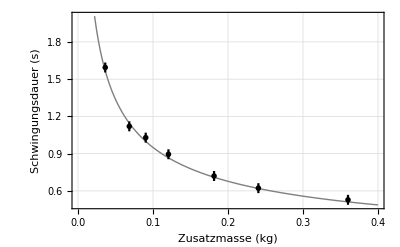

```mathematica
Needs["ErrorBarPlots`"]

SetOptions[Plot,BaseStyle->{FontFamily->"Times New Roman",FontSize->9}];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times New Roman",FontSize->9}]; (* larger FontSize for tick labels *)
al={FontSize->11,Black}; (* style for axis labels *)

e=ErrorBar[0.04]; (* absolute error for period *)

data={{{0.36,0.528},e},{{0.2405,0.622},e},{{0.1814,0.720},e},{{0.1206,0.895},e},{{0.0903,1.029},e},{{0.0684,1.120},e},{{0.0363,1.594},e}}; (* measured data: {m,T} *)

ω:=Sqrt[r g γ(M+m)/(J+(m+M)(Ro-γ r)^2)] (* angular frequency *)
T:=2 Pi/ω (* period *)

Show[{Plot[T,{m,0,0.4},PlotStyle->{Gray,Thick}],ErrorListPlot[data,PlotStyle->{Black,PointSize->0.01}]},Frame->True,GridLines->Automatic,FrameLabel->{Style["Zusatzmasse (kg)",al],Style["Schwingungsdauer (s)",al]},ImageSize->{270 GoldenRatio,270}]
```

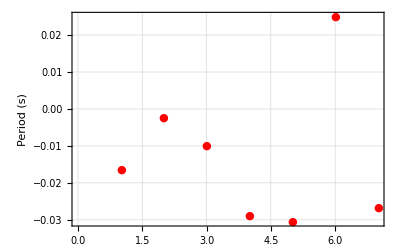

```mathematica
residuals=Table[{{i,T-data[[i,1,2]]/.m->data[[i,1,1]]},data[[i,2]]},{i,1,Length[data]}]; (* residuals for period *)

ErrorListPlot[residuals,PlotMarkers->{Automatic,Medium},PlotStyle->{Red,Thick},Frame->True,GridLines->Automatic,FrameLabel->{None,Style["Period (s)",al]},ImageSize->{350 GoldenRatio,350}] (* plot residuals *)
```

```mathematica
?ErrorListPlot
```

ErrorListPlot[{{y_1,dy_1},{y_2,dy_2},…}] plots points corresponding to a list of values y_1, y_2, …, with corresponding error bars. The errors have magnitudes dy_1,dy_2,….
ErrorListPlot[{{{x_1,y_1},ErrorBar[err_1]},{{x_2,y_2},ErrorBar[err_2]},…}] plots points with specified x and y coordinates and error magnitudes.

```mathematica
Acrylic Glass (Large)
```

```mathematica
Clear[M,m,R,r,γ,g,J]

M=0.1666; (* mass of ring *)
Ro=0.12/2; (* outer radius ring *)
Ri = 0.1145/2; (* inner radius ring *)

d=0.014; (* diameter extra mass *)
r=Ri-d/2;(* position extra mass *)
γ:=m/(M+m) (* relative position centre of mass *)
g=9.81; (* gravitational acceleration *)

JM=M((Ro^2+Ri^2)/2+(γ r)^2); (* moment of inertia for ring *)
Jm:=m ((1-γ)r)^2 (* moment of inertia for extra mass *)

J:=JM+Jm (* total moment of inertia *)
```

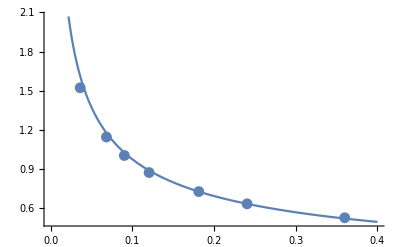

```mathematica
Needs["ErrorBarPlots`"]
e:=ErrorBar[0.02];
data={{{0.36,0.524},e},{{0.2405,0.631},e},{{0.1814,0.725},e},{{0.1206,0.871},e},{{0.0903, 1.002}, e}, {{0.0684, 1.144}, e}, {{0.0363, 1.522}, e}}; (* measured data: {m,T} *)
ω:=Sqrt[r g γ(M+m)/(J+(m+M)(Ro-γ r)^2)] (* angular frequency *)
T:=2 Pi/ω (* period *)
Show[{Plot[T,{m,0,0.4}],ErrorListPlot[data]}]
```

```mathematica
Dark Grey Plastic (Large)
```

```mathematica
Clear[M,m,R,r,γ,g,J]

M=0.194; (* mass of ring *)
Ro=0.111/2; (* outer radius ring *)
Ri = 0.103/2; (* inner radius ring *)

d=0.014; (* diameter extra mass *)
r=Ri-d/2;(* position extra mass *)
γ:=m/(M+m) (* relative position centre of mass *)
g=9.81; (* gravitational acceleration *)

JM=M((Ro^2+Ri^2)/2+(γ r)^2); (* moment of inertia for ring *)
Jm:=m ((1-γ)r)^2 (* moment of inertia for extra mass *)

J:=JM+Jm (* total moment of inertia *)
```

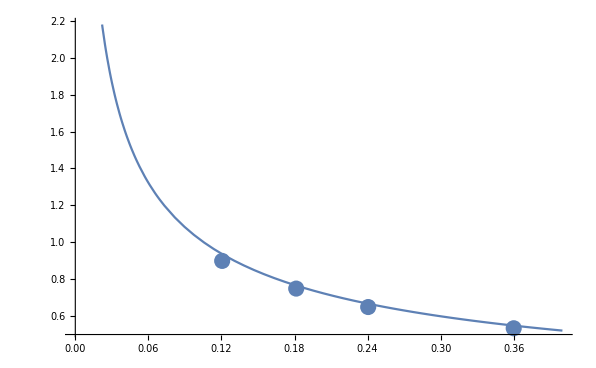

```mathematica
Needs["ErrorBarPlots`"]
e:=ErrorBar[0.02];
data={{{0.36,0.534},e},{{0.2405,0.649},e},{{0.1814,0.749},e},{{0.1206,0.899},e}}; (* measured data: {m,T} *)
ω:=Sqrt[r g γ(M+m)/(J+(m+M)(Ro-γ r)^2)] (* angular frequency *)
T:=2 Pi/ω (* period *)
Show[{Plot[T,{m,0,0.4}],ErrorListPlot[data]}]
```

```mathematica
Large11
```

```mathematica
Clear[M,m,R,r,γ,g,J]

M=0.4195; (* mass of ring *)
Ro=0.1985/2; (* outer radius ring *)
Ri = 0.1895/2; (* inner radius ring *)

d=0.014; (* diameter extra mass *)
r=Ri-d/2;(* position extra mass *)
γ:=m/(M+m) (* relative position centre of mass *)
g=9.81; (* gravitational acceleration *)

JM=M((Ro^2+Ri^2)/2+(γ r)^2); (* moment of inertia for ring *)
Jm:=m ((1-γ)r)^2 (* moment of inertia for extra mass *)

J:=JM+Jm (* total moment of inertia *)
```

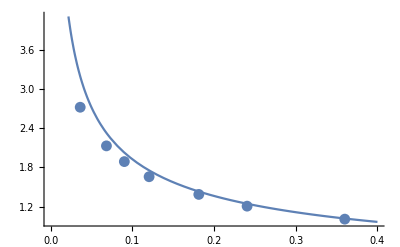

```mathematica
Needs["ErrorBarPlots`"]
e:=ErrorBar[0.02];
data={{{0.36,1.008},e},{{0.2405,1.207},e},{{0.1814,1.387},e},{{0.1206,1.658},e}, {{0.0903, 1.890}, e}, {{0.0684, 2.131}, e}, {{0.0363, 2.723}, e}}; (* measured data: {m,T} *)
ω:=Sqrt[r g γ(M+m)/(J+(m+M)(Ro-γ r)^2)] (* angular frequency *)
T:=2 Pi/ω (* period *)
Show[{Plot[T,{m,0,0.4}],ErrorListPlot[data]}]
```